```mathematica
a={Arrowheads[Large],Arrow[{{0,0},{1,.5}}]};
```

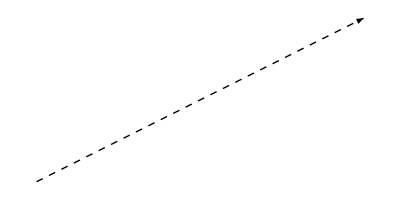
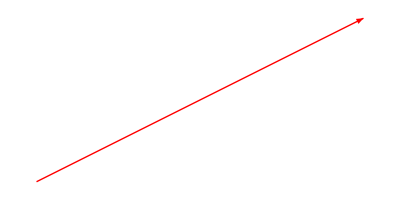
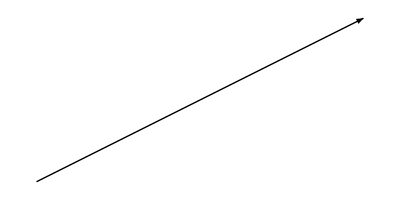
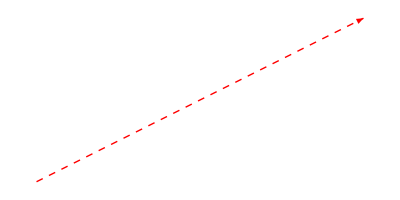

```mathematica
{Graphics[{Dashed,a}],Graphics[{Red,a}],Graphics[{Thick,a}],Graphics[{Thick,Dashed,Red,a}]}
```

```mathematica
Graphics
```

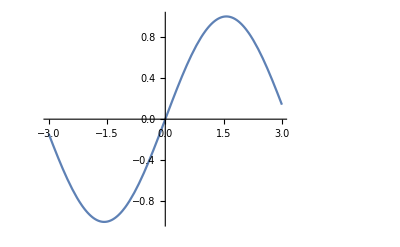

```mathematica
Plot[Sin[x],{x,-3,3},Epilog->{Arrow[{{0,0,{√2,√2}}],Text["Zero",{3Pi/2,1/2},{-1,-1}]}]
```

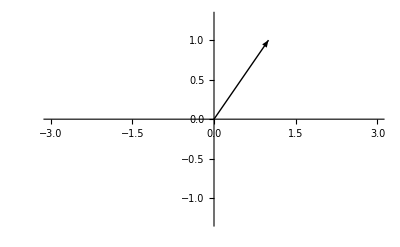

```mathematica
Plot[Sin[x],{x,-3,3},PlotRange->1.3,ColorFunction->Function[{x,y},RGBColor[1,1,1]],Epilog->{Arrow[{{0,0},{1,1}}]}]
```

```mathematica
PlotVec[x1_,y1_]:=Plot[x,{x,-3,3},PlotRange->1,ColorFunction->Function[{x,y},RGBColor[1,1,1]],Epilog->{{Thick,{Arrowheads[Large],Arrow[{{0,0},{x1,y1}}]}}}]
```

```mathematica
Manipulate[PlotVec[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
PlotVec2[θ_]:=Plot[x,{x,-1,1},PlotRange->1,AspectRatio->1,ColorFunction->Function[{x,y},RGBColor[1,1,1]],Epilog->{{Thick,{Arrowheads[Large],Arrow[{{0,0},{Cos[θ],Sin[θ]}}]}}}];
Manipulate[PlotVec2[θ],{θ,-2π,2π}]
```

```mathematica
flipmatrix[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}});
```

```mathematica
flipmatrix[π/4]. ({{1}, {1}})//MatrixForm
```

(0
√2)

```mathematica
flipmatrix[θ]. ({{x1, x2}, {y1, y2}})//MatrixForm
```

(x1 Cos[θ]-y1 Sin[θ] | x2 Cos[θ]-y2 Sin[θ]
y1 Cos[θ]+x1 Sin[θ] | y2 Cos[θ]+x2 Sin[θ])

```mathematica
y1
```

y1

```mathematica
flipmatrix[π/4]. ({{-1}, {1}})//MatrixForm
```

(-√2
0)

```mathematica
flipmatrix[π/4]//MatrixForm
```

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

```mathematica
flipvec[({{x_}, {y_}}),θ_]:=(flipmatrix[θ].({{x}, {y}}))//MatrixForm
```

```mathematica
flip
```

```mathematica
({{1}, {1}})
```

{{1},{1}}

```mathematica
Flatten[{{0},{√2}}]
```

{0,√2}

```mathematica
{{1},{1}} .{{1,1}}
```

{{1,1},{1,1}}

```mathematica
PlotVec3[θ_,ϕ_]:=Plot[x,{x,-1,1},PlotRange->1,AspectRatio->1,ColorFunction->Function[{x,y},RGBColor[1,1,1]],Epilog->{{Thick,{Red,Arrowheads[Large],Arrow[{{0,0},{Cos[θ],Sin[θ]}}]},{Arrowheads[Large],Arrow[{{0,0},Flatten[flipmatrix[-ϕ].(List/@{Cos[θ],Sin[θ]})] }]}}}];
Manipulate[PlotVec3[π/4,ϕ],{ϕ,0,2π,π/4}]
```

```mathematica
π/4
```

```mathematica
Flatten[flipmatrix[-π/2].(List/@{Cos[θ],Sin[θ]})]
```

{Sin[θ],-Cos[θ]}

```mathematica
MatrixForm[{{Sin[θ]},{-Cos[θ]}}]
```

(Sin[θ]
-Cos[θ])

```mathematica
MatrixForm[{{Cos[θ]},{Sin[θ]}}]
```

(Cos[θ]
Sin[θ])

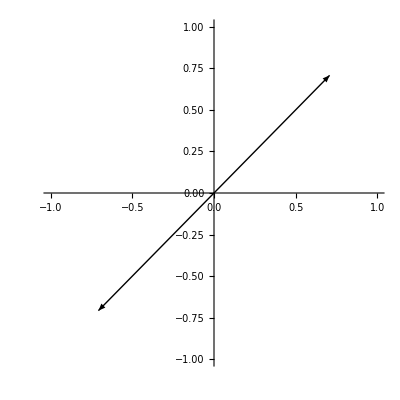

```mathematica
PlotVec3[π/4]
```

```mathematica
MatrixM
```

```mathematica
Cos[Pi/2]+Sin[Pi/2]
```

1

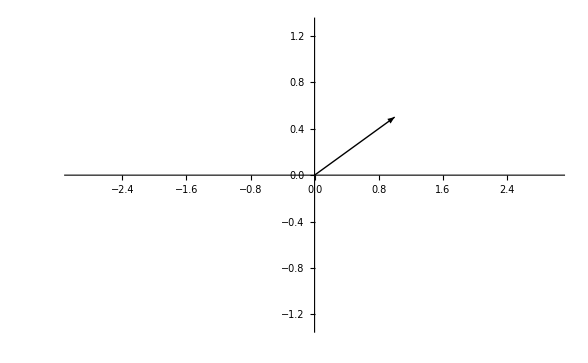

```mathematica
PlotVec[x1_,y1_]:=Plot[x,{x,-3,3},PlotRange->1.3,ColorFunction->Function[{x,y},RGBColor[1,1,1]],Epilog->{{Thick,{Arrowheads[Large],Arrow[{{0,0},{x1,y1}}]}}}]
```

```mathematica
RGBColor[1,1,1]
```

RGBColor[1, 1, 1]